```mathematica
SetDirectory["/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/ConvexHull/Helpers/Text files"];
coordinatesPath = "coordinates.txt";
firstMethodPath = "ConvexHullPoints(MethodI).txt";
secondMethodPath = "ConvexHullPoints(MethodII).txt";
```

```mathematica
getPointsFrom[filePath_String] := Module[{points},
points = ReadList[filePath, Real];
points = Delete[points, {1}];
 Partition[points, 2]
]
```

```mathematica
inputPoints = Point[#]&/@ getPointsFrom[coordinatesPath];
pointsToBeConnected = getPointsFrom[firstMethodPath];
firstAlgorithmPoints = Line@Join[pointsToBeConnected, {pointsToBeConnected[[1]]}];
kirkpatrickSeidelConvexHullPoints = Line@getPointsFrom[secondMethodPath];
```

# Coordinates

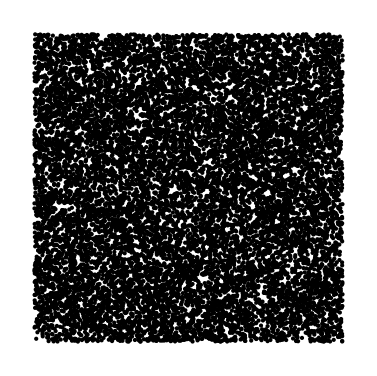

```mathematica
Graphics[inputPoints]
```

# First Method

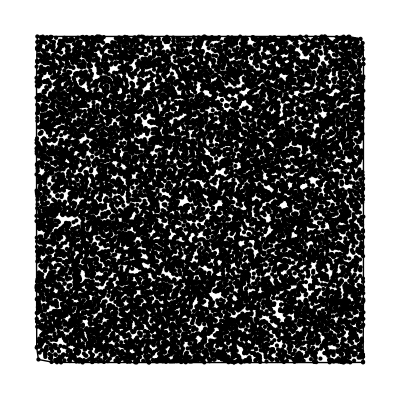

```mathematica
Graphics[{inputPoints, firstAlgorithmPoints}]
```

# Kirkpatrcik-Seidel Algorithm

```mathematica
Graphics[{inputPoints, kirkpatrickSeidelConvexHullPoints}]
```

-Graphics-